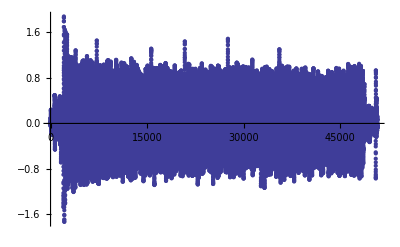

```mathematica
ListPlot[applyhighpassfilter[getData[dataproc,1,"Roll Angular Velocity"],1000]]
```

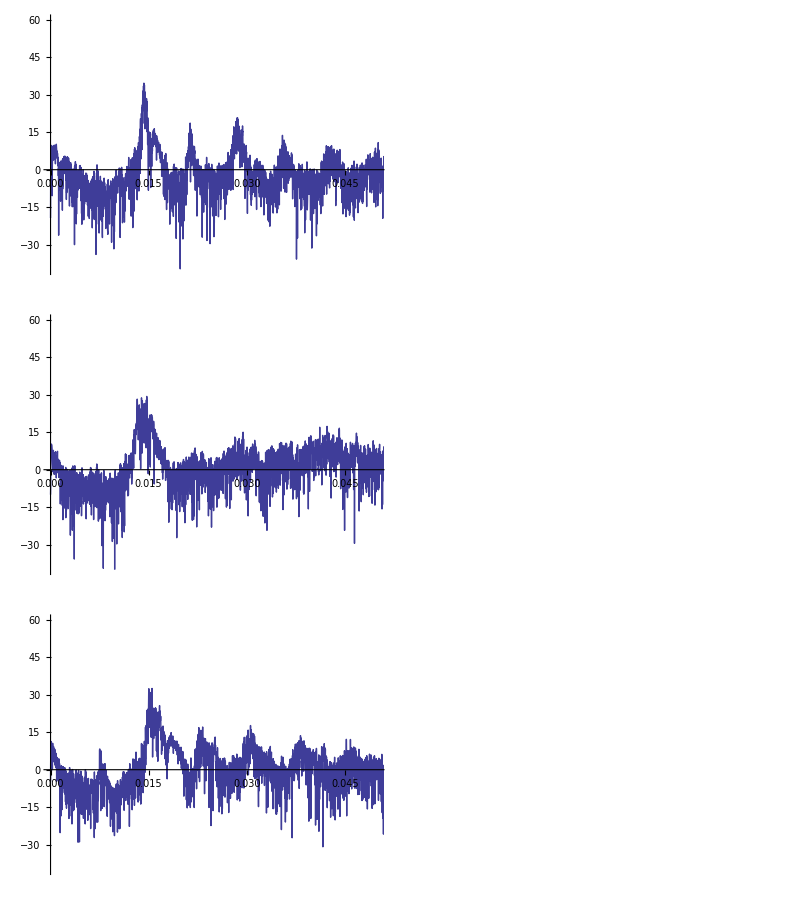

```mathematica
serie="Forward Acceleration";
TableForm[Table[{Periodogram[getData[dataproc,i,serie],PlotRange->{{0,0.05},{-40,60}},ImageSize->400],ListPlay[resize[applyhighpassfilter[getData[dataproc,i,serie],500],120000],PlayRange->All,SampleRate->44100]},{i,1,3,1}]]
```

```mathematica
ListPlay[resize[applyhighpassfilter[getData[dataproc,1,"Pitch Angular Acceleration"],500],88100],SampleRate->44100]
```

-Graphics-